Расчеты

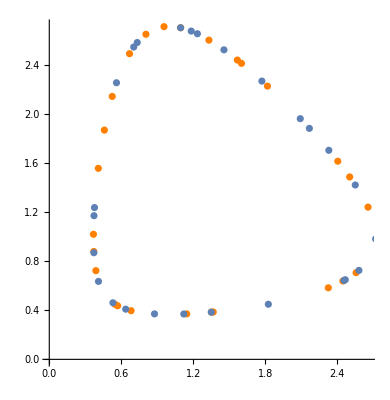

0.00638225

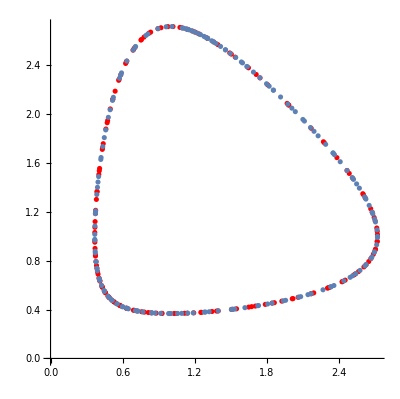

0.000195574

```mathematica
t1 = 0.3; t2 = t1 + 4;
y1[t_]:=Exp[Sin[t^2]]; y2[t_]:= Exp[Cos[t^2]];
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm\\plot"];
datRK= Import["RK4.dat"];
datDP= Import["DP4_5.dat"];

listRK= {};
For[i = 1, i <= Length[datRK]-1, ++i,
AppendTo[listRK, {datRK[[i,2]], datRK[[i,3]]}]]
listDP= {};
For[i = 1, i <= Length[datDP]-1, ++i,
AppendTo[listDP, {datDP[[i,2]], datDP[[i,3]]}]]

listRKA = {};
tau = 4/(Length[listRK]-1);
For[ t= 0.3, t <= 4.3, t+=tau,
AppendTo[listRKA, {y1[t], y2[t]}]]
listRKAC= {};
For[i = 1, i <= Length[listRK], ++i,
AppendTo[listRKAC, {y1[datRK[[i,1]]], y2[datRK[[i,1]]]}]]
listDPA = {};
tau = 4/(Length[listDP]-1);
For[ t= 0.3, t <= 4.3, t+=tau,
AppendTo[listDPA, {y1[t], y2[t]}]]
listDPAC= {};
For[i = 1, i <= Length[listDP], ++i,
AppendTo[listDPAC, {y1[datDP[[i,1]]], y2[datDP[[i,1]]]}]]

LRK= ListPlot[listRK, PlotStyle->Orange, AspectRatio->Automatic];
LDP= ListPlot[listDP, PlotStyle->Red, AspectRatio->Automatic];
LRKA= ListPlot[listRKA , AspectRatio->Automatic];
LDPA= ListPlot[listDPA, AspectRatio->Automatic];
Show[LRK, LRKA]
Norm[listRK - listRKAC]
Show[LDP, LDPA]
Norm[listDP - listDPAC]
```

Выводы задания 1

```mathematica
(*Все переменные, кроме варьируемой, зафиксированы: tau = 0.1, fac = 0.8, facmin = 0.4, facmax = 3*)
```

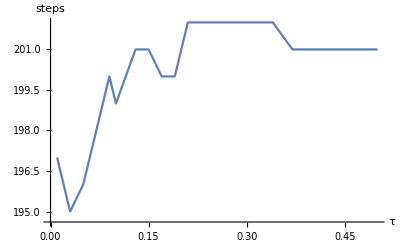

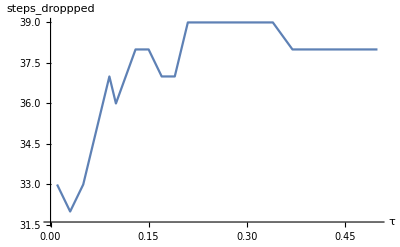

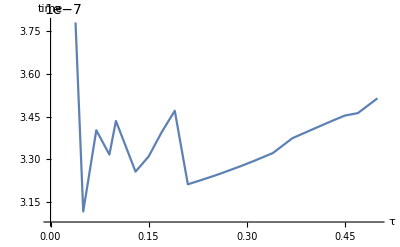

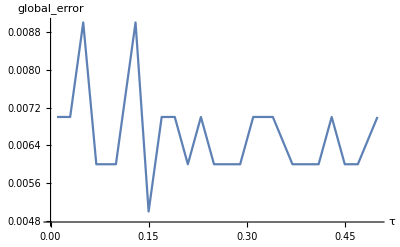

```mathematica
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm\\plot"];
taud= Import["tau.dat"];
tauplotST = {};
tauplotSTD = {};
tauplotTIME = {};
tauplotERR = {};
For[i = 1, i <= Length[taud],i++,
AppendTo[tauplotST,{taud[[i,1]],taud[[i,5]]}];
AppendTo[tauplotSTD,{taud[[i,1]],taud[[i,6]]}];
AppendTo[tauplotTIME,{taud[[i,1]],taud[[i,7]]}];
AppendTo[tauplotERR,{taud[[i,1]],taud[[i,8]]}];]
ListLinePlot[tauplotST, AxesLabel->{"τ","steps"}]
ListLinePlot[tauplotSTD, AxesLabel->{"τ","steps_droppped"}]
ListLinePlot[tauplotTIME, AxesLabel->{"τ","time"}]
ListLinePlot[tauplotERR, AxesLabel->{"τ","global_error"}]
```

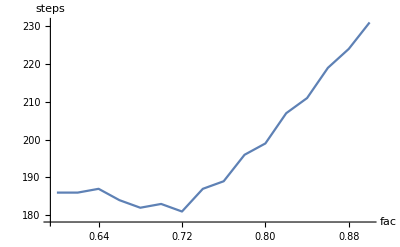

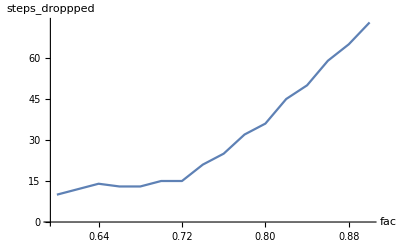

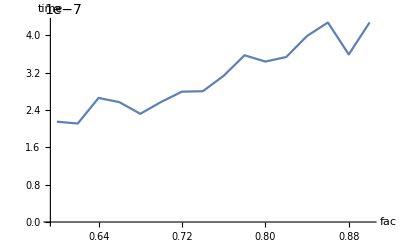

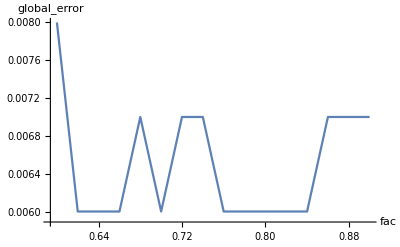

```mathematica
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm\\plot"];
facd= Import["fac.dat"];
facplotST = {};
facplotSTD = {};
facplotTIME = {};
facplotERR = {};
For[i = 1, i <= Length[facd],i++,
AppendTo[facplotST,{facd[[i,2]],facd[[i,5]]}];
AppendTo[facplotSTD,{facd[[i,2]],facd[[i,6]]}];
AppendTo[facplotTIME,{facd[[i,2]],facd[[i,7]]}];
AppendTo[facplotERR,{facd[[i,2]],facd[[i,8]]}];]
ListLinePlot[facplotST, AxesLabel->{"fac","steps"}]
ListLinePlot[facplotSTD, AxesLabel->{"fac","steps_droppped"}]
ListLinePlot[facplotTIME, AxesLabel->{"fac","time"}]
ListLinePlot[facplotERR, AxesLabel->{"fac","global_error"}]
```

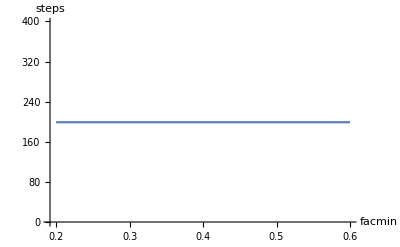

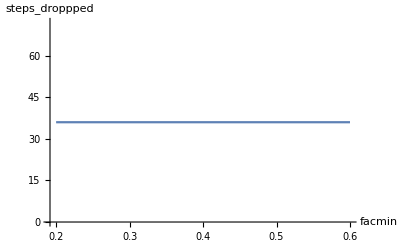

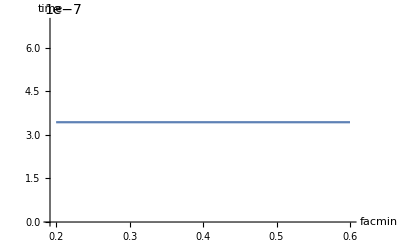

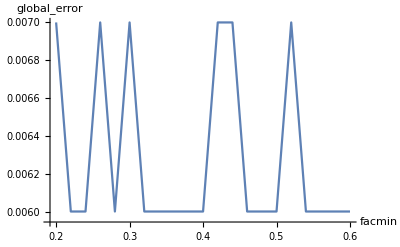

```mathematica
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm\\plot"];
facmind= Import["facmin.dat"];
facminplotST = {};
facminplotSTD = {};
facminplotTIME = {};
facminplotERR = {};
For[i = 1, i <= Length[facmind],i++,
AppendTo[facminplotST,{facmind[[i,3]],facmind[[i,5]]}];
AppendTo[facminplotSTD,{facmind[[i,3]],facmind[[i,6]]}];
AppendTo[facminplotTIME,{facmind[[i,3]],facmind[[i,7]]}];
AppendTo[facminplotERR,{facmind[[i,3]],facmind[[i,8]]}];]
ListLinePlot[facminplotST, AxesLabel->{"facmin","steps"}]
ListLinePlot[facminplotSTD, AxesLabel->{"facmin","steps_droppped"}]
ListLinePlot[facminplotTIME, AxesLabel->{"facmin","time"}]
ListLinePlot[facminplotERR, AxesLabel->{"facmin","global_error"}]
```

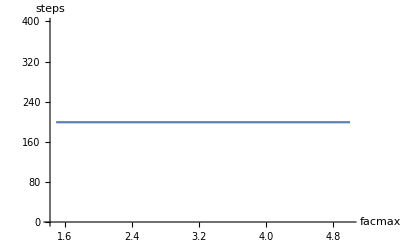

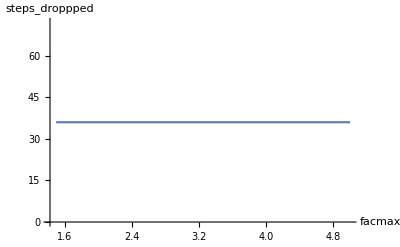

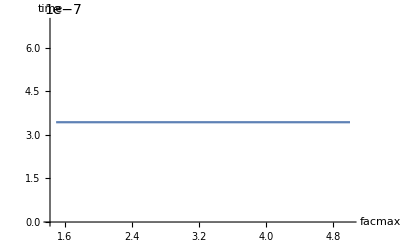

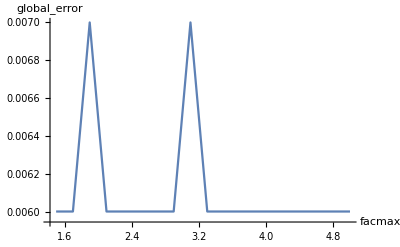

```mathematica
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm\\plot"];
facmaxd= Import["facmax.dat"];
facmaxplotST = {};
facmaxplotSTD = {};
facmaxplotTIME = {};
facmaxplotERR = {};
For[i = 1, i <= Length[facmaxd],i++,
AppendTo[facmaxplotST,{facmaxd[[i,4]],facmaxd[[i,5]]}];
AppendTo[facmaxplotSTD,{facmaxd[[i,4]],facmaxd[[i,6]]}];
AppendTo[facmaxplotTIME,{facmaxd[[i,4]],facmaxd[[i,7]]}];
AppendTo[facmaxplotERR,{facmaxd[[i,4]],facmaxd[[i,8]]}];]
ListLinePlot[facmaxplotST, AxesLabel->{"facmax","steps"}]
ListLinePlot[facmaxplotSTD, AxesLabel->{"facmax","steps_droppped"}]
ListLinePlot[facmaxplotTIME, AxesLabel->{"facmax","time"}]
ListLinePlot[facmaxplotERR, AxesLabel->{"facmax","global_error"}]
```

Выводы задания 2

```mathematica
(*tau = 0.1, fac = 0.8, facmin = 0.4, facmax = 3*)
(**)
```

Рунге-Кутта |  |  | 
tol | 10^-3 | 10^-4 | 10^-5
st | 28 | 44 | 99
st_dropped | 3 | 5 | 2
global_error | 0.00105959 | 0.00067775 | 9.31457×10^-6
time | 0.001 | 0.002 | 0.003

Дорман-Принс |  |  | 
tol | 10^-3 | 10^-4 | 10^-5
st | 106 | 199 | 765
st_dropped | 28 | 36 | 21
global_error | 0.0000112018 | 3.43449×10^-7 | 1.39698×10^-10
time | 0.003 | 0.006 | 0.025

Методы Рунге-Кутты

tol = 10^-3

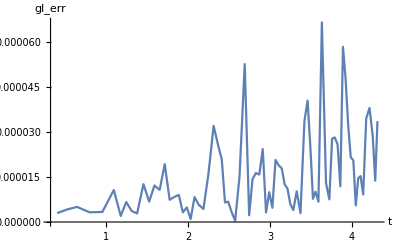

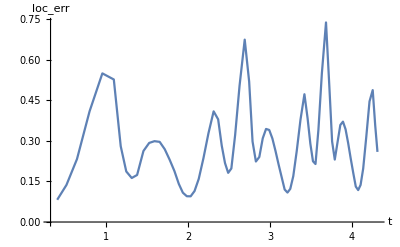

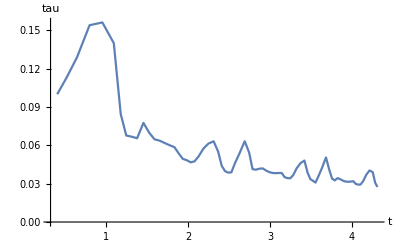

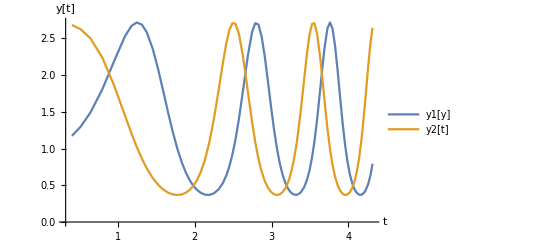

tol = 10^-4

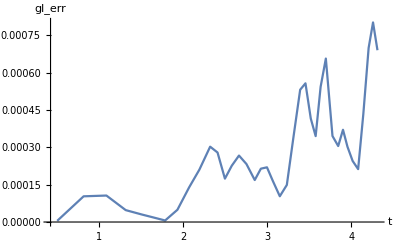

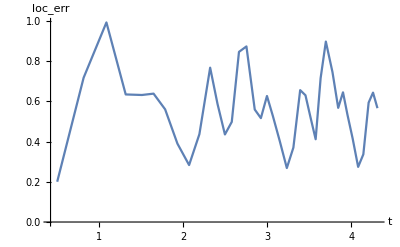

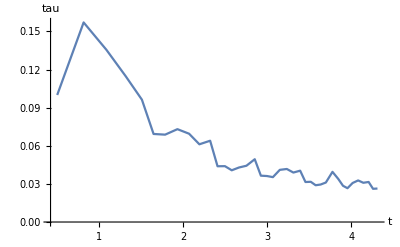

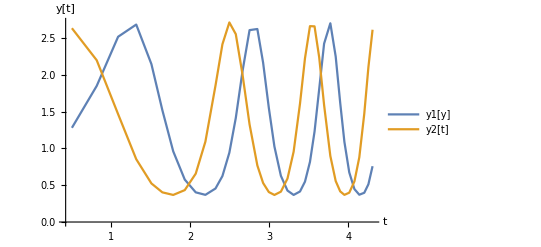

tol = 10^-6

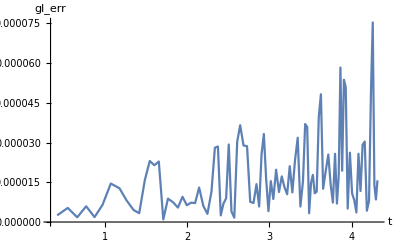

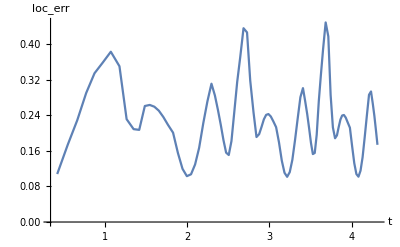

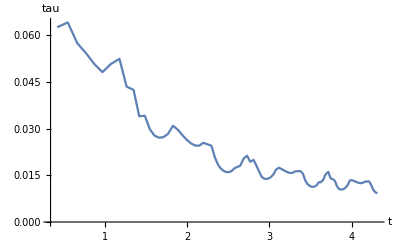

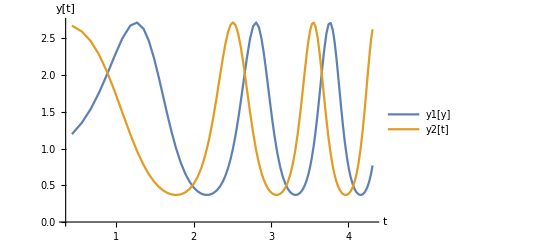

Методы Дормана-Принса

tol = 10^-3

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

tol = 10^-4

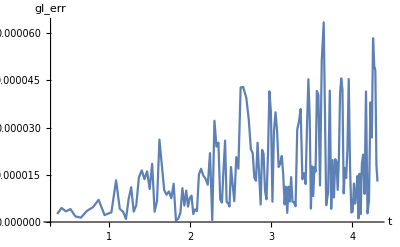

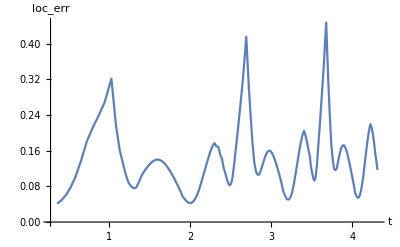

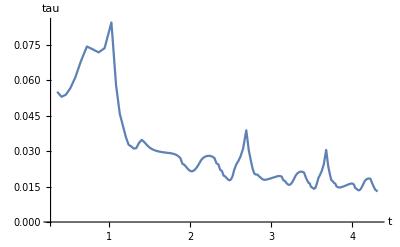

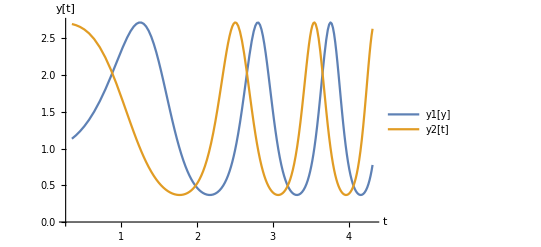

tol = 10^-6

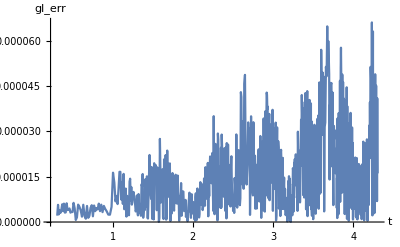

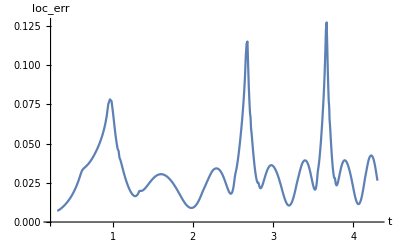

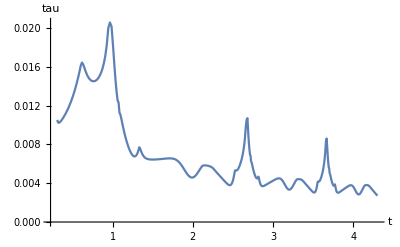

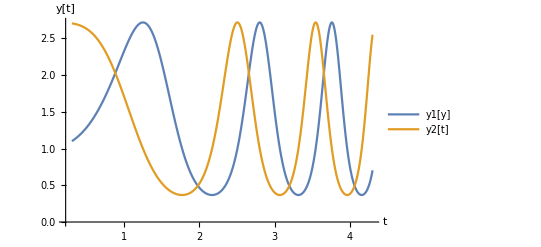

```mathematica
y1[t_]:=Exp[Sin[t^2]]; y2[t_]:= Exp[Cos[t^2]];
SetDirectory["D:\\BMSTU\\5th_term\\4 semestr\\Rodin\\DZ\\DZ\\programm\\plot"];
rkdat= Import["rk.dat"];
dpdat= Import["dp.dat"];
Grid[{{Text["Рунге-Кутта"],SpanFromLeft},{"tol","10^-3","10^-4","10^-5"},
{"st",rkdat[[1,5]], rkdat[[2,5]], rkdat[[3,5]]},
{"st_dropped", rkdat[[1,6]], rkdat[[2,6]], rkdat[[3,6]]},
{"global_error", rkdat[[1,7]], rkdat[[2,7]], rkdat[[3,7]]},
{"time", rkdat[[1,8]], rkdat[[2,8]], rkdat[[3,8]]}},Frame->All]
Grid[{{Text["Дорман-Принс"],SpanFromLeft},{"tol","10^-3","10^-4","10^-5"},
{"st",dpdat[[1,5]], dpdat[[2,5]], dpdat[[3,5]]},
{"st_dropped", dpdat[[1,6]], dpdat[[2,6]], dpdat[[3,6]]},
{"global_error", dpdat[[1,7]], dpdat[[2,7]], dpdat[[3,7]]},
{"time", dpdat[[1,8]], dpdat[[2,8]], dpdat[[3,8]]}},Frame->All]
rk3d = Import["RK4-3.dat"];
rk4d = Import["RK4-4.dat"];
rk6d = Import["RK4-6.dat"];
rk3d = Import["DP4_5-3.dat"];
dp4d = Import["DP4_5-4.dat"];
dp6d = Import["DP4_5-6.dat"];
rk3gl = {}; rk3loc = {}; rk3tau = {}; rk3x = {}; rk3y = {};
rk4gl = {}; rk4loc = {}; rk4tau = {}; rk4x = {}; rk4y = {};
rk6gl = {}; rk6loc = {}; rk6tau = {}; rk6x = {}; rk6y = {};
dp3gl = {}; dp3loc = {}; dp3tau = {}; dp3x = {}; dp3y = {};
dp4gl = {}; dp4loc = {}; dp4tau = {}; dp4x = {}; dp4y = {};
dp6gl = {}; dp6loc = {}; dp6tau = {}; dp6x = {}; dp6y = {};
For[i = 2,i <= Length[rk3d]-1,++i,
gl = √((rk3d[[i,2]] - y1[rk3d[[i,1]]])^2+(rk3d[[i,3]] - y2[rk3d[[i,1]]])^2);
loc = √((rk3d[[i,2]] - rk3d[[i-1,2]])^2+(rk3d[[i,3]] - rk3d[[i-1,3]])^2);
AppendTo[rk3gl,{rk3d[[i,1]], gl}];
AppendTo[rk3loc,{rk3d[[i,1]], loc}];
AppendTo[rk3tau,{rk3d[[i,1]], rk3d[[i,-1]]}];
AppendTo[rk3x,{rk3d[[i,1]], rk3d[[i,2]]}];
AppendTo[rk3y,{rk3d[[i,1]], rk3d[[i,3]]}];
]
For[i = 2,i <= Length[rk4d]-1,++i,
gl = √((rk4d[[i,2]] - y1[rk4d[[i,1]]])^2+(rk4d[[i,3]] - y2[rk4d[[i,1]]])^2);
loc = √((rk4d[[i,2]] - rk4d[[i-1,2]])^2+(rk4d[[i,3]] - rk4d[[i-1,3]])^2);
AppendTo[rk4gl,{rk4d[[i,1]], gl}];
AppendTo[rk4loc,{rk4d[[i,1]], loc}];
AppendTo[rk4tau,{rk4d[[i,1]], rk4d[[i,-1]]}];
AppendTo[rk4x,{rk4d[[i,1]], rk4d[[i,2]]}];
AppendTo[rk4y,{rk4d[[i,1]], rk4d[[i,3]]}];
]
For[i = 2,i <= Length[rk6d]-1,++i,
gl = √((rk6d[[i,2]] - y1[rk6d[[i,1]]])^2+(rk6d[[i,3]] - y2[rk6d[[i,1]]])^2);
loc = √((rk6d[[i,2]] - rk6d[[i-1,2]])^2+(rk6d[[i,3]] - rk6d[[i-1,3]])^2);
AppendTo[rk6gl,{rk6d[[i,1]], gl}];
AppendTo[rk6loc,{rk6d[[i,1]], loc}];
AppendTo[rk6tau,{rk6d[[i,1]], rk6d[[i,-1]]}];
AppendTo[rk6x,{rk6d[[i,1]], rk6d[[i,2]]}];
AppendTo[rk6y,{rk6d[[i,1]], rk6d[[i,3]]}];
]

Print[Style["Методы Рунге-Кутты",22,Blue]]
Print[Style["tol = 10^-3",18,Blue]]
ListLinePlot[rk3gl, AxesLabel->{"t", "gl_err"},PlotRange->All]
ListLinePlot[rk3loc, AxesLabel->{"t", "loc_err"},PlotRange->All]
ListLinePlot[rk3tau, AxesLabel->{"t", "tau"},PlotRange->All]
ListLinePlot[{rk3x, rk3y}, AxesLabel->{"t", "y[t]"},PlotLegends->{"y1[y]","y2[t]"},PlotRange->All]
Print[Style["tol = 10^-4",18,Blue]]
ListLinePlot[rk4gl, AxesLabel->{"t", "gl_err"},PlotRange->All]
ListLinePlot[rk4loc, AxesLabel->{"t", "loc_err"},PlotRange->All]
ListLinePlot[rk4tau, AxesLabel->{"t", "tau"},PlotRange->All]
ListLinePlot[{rk4x, rk4y}, AxesLabel->{"t", "y[t]"},PlotLegends->{"y1[y]","y2[t]"},PlotRange->All]
Print[Style["tol = 10^-6",18,Blue]]
ListLinePlot[rk6gl, AxesLabel->{"t", "gl_err"},PlotRange->All]
ListLinePlot[rk6loc, AxesLabel->{"t", "loc_err"},PlotRange->All]
ListLinePlot[rk6tau, AxesLabel->{"t", "tau"},PlotRange->All]
ListLinePlot[{rk6x, rk6y}, AxesLabel->{"t", "y[t]"},PlotLegends->{"y1[y]","y2[t]"},PlotRange->All]

(****)
For[i = 2,i <= Length[dp3d]-1,++i,
gl = √((dp3d[[i,2]] - y1[dp3d[[i,1]]])^2+(dp3d[[i,3]] - y2[dp3d[[i,1]]])^2);
loc = √((dp3d[[i,2]] - dp3d[[i-1,2]])^2+(dp3d[[i,3]] - dp3d[[i-1,3]])^2);
AppendTo[dp3gl,{dp3d[[i,1]], gl}];
AppendTo[dp3loc,{dp3d[[i,1]], loc}];
AppendTo[dp3tau,{dp3d[[i,1]], dp3d[[i,-1]]}];
AppendTo[dp3x,{dp3d[[i,1]], dp3d[[i,2]]}];
AppendTo[dp3y,{dp3d[[i,1]], dp3d[[i,3]]}];
]
For[i = 2,i <= Length[dp4d]-1,++i,
gl = √((dp4d[[i,2]] - y1[dp4d[[i,1]]])^2+(dp4d[[i,3]] - y2[dp4d[[i,1]]])^2);
loc = √((dp4d[[i,2]] - dp4d[[i-1,2]])^2+(dp4d[[i,3]] - dp4d[[i-1,3]])^2);
AppendTo[dp4gl,{dp4d[[i,1]], gl}];
AppendTo[dp4loc,{dp4d[[i,1]], loc}];
AppendTo[dp4tau,{dp4d[[i,1]], dp4d[[i,-1]]}];
AppendTo[dp4x,{dp4d[[i,1]], dp4d[[i,2]]}];
AppendTo[dp4y,{dp4d[[i,1]], dp4d[[i,3]]}];
]
For[i = 2,i <= Length[dp6d]-1,++i,
gl = √((dp6d[[i,2]] - y1[dp6d[[i,1]]])^2+(dp6d[[i,3]] - y2[dp6d[[i,1]]])^2);
loc = √((dp6d[[i,2]] - dp6d[[i-1,2]])^2+(dp6d[[i,3]] - dp6d[[i-1,3]])^2);
AppendTo[dp6gl,{dp6d[[i,1]], gl}];
AppendTo[dp6loc,{dp6d[[i,1]], loc}];
AppendTo[dp6tau,{dp6d[[i,1]], dp6d[[i,-1]]}];
AppendTo[dp6x,{dp6d[[i,1]], dp6d[[i,2]]}];
AppendTo[dp6y,{dp6d[[i,1]], dp6d[[i,3]]}];
]

Print[Style["Методы Дормана-Принса",22,Red]]
Print[Style["tol = 10^-3",18,Red]]
ListLinePlot[dp3gl, AxesLabel->{"t", "gl_err"},PlotRange->All]
ListLinePlot[dp3loc, AxesLabel->{"t", "loc_err"},PlotRange->All]
ListLinePlot[dp3tau, AxesLabel->{"t", "tau"},PlotRange->All]
ListLinePlot[{dp3x, dp3y}, AxesLabel->{"t", "y[t]"},PlotLegends->{"y1[y]","y2[t]"},PlotRange->All]
Print[Style["tol = 10^-4",18,Red]]
ListLinePlot[dp4gl, AxesLabel->{"t", "gl_err"},PlotRange->All]
ListLinePlot[dp4loc, AxesLabel->{"t", "loc_err"},PlotRange->All]
ListLinePlot[dp4tau, AxesLabel->{"t", "tau"},PlotRange->All]
ListLinePlot[{dp4x, dp4y}, AxesLabel->{"t", "y[t]"},PlotLegends->{"y1[y]","y2[t]"},PlotRange->All]
Print[Style["tol = 10^-6",18,Red]]
ListLinePlot[dp6gl, AxesLabel->{"t", "gl_err"},PlotRange->All]
ListLinePlot[dp6loc, AxesLabel->{"t", "loc_err"},PlotRange->All]
ListLinePlot[dp6tau, AxesLabel->{"t", "tau"},PlotRange->All]
ListLinePlot[{dp6x, dp6y}, AxesLabel->{"t", "y[t]"},PlotLegends->{"y1[y]","y2[t]"},PlotRange->All]
```